```mathematica
sol=DSolve[{D[y[x],{x,2}]==-4y[x],y[0]==10,y'[0]==1},y[x],x]
```

{{y[x]→1/2 (20 Cos[2 x]+Sin[2 x])}}

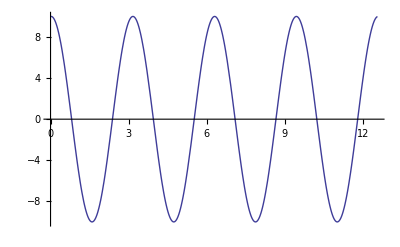

```mathematica
Plot[y[x]/.sol,{x,0,4Pi}]
```

```mathematica
val=Range[0,4Pi,4Pi/100];
```

```mathematica
t=Flatten[N@Table[y[x]/.sol,{x,0,4Pi,4Pi/100}]];
```

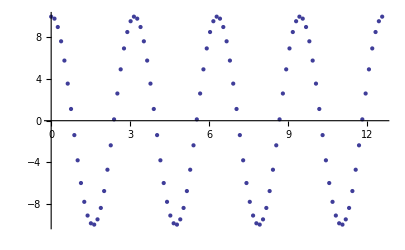

```mathematica
ListPlot[Partition[Riffle[val,t],2]]
```